## Towards a Minimal Model for Computer Security

Willem Nielsen

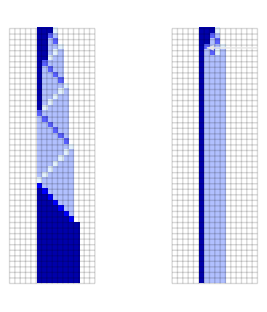

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
{ca, capert} = First[[rule, {Join[Table[1,3],{2}],0},{45,{-5, 10}}, #]]&/@ {<||>, pert};
GraphicsRow[MapThread[{{"[◼]", "PerturbedArrayPlot"}}[#1, #2,ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.15], "ArrowStyle"->Directive[Arrowheads[Medium],GrayLevel[.9], Haloing[Red, 1.25]],"ArrowDirection"->Left, "InitialIndex"->0] &,{{ca, capert},  {{}, First[Keys[pert]]}}
], Spacings->{60, 60}, Frame->True,FrameStyle->GrayLevel[.7], ImageSize->{300, 350}]]
```

## Background

## Cellular Automata: A Model for Biological Organisms

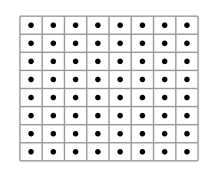
-Graphics--Graphics-

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},110],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.1]],RulePlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

## The Concept of Disease: Perturbing the Organism

## Modeling a Software System: Doubling Procedure

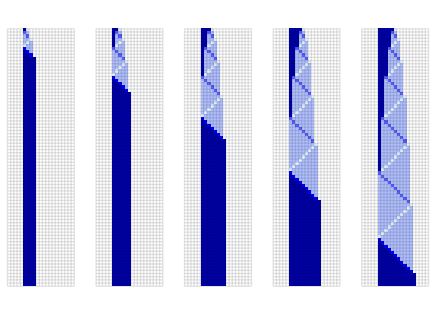

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[1]]
]
```

## Modeling an Attacker: Perturbing the System

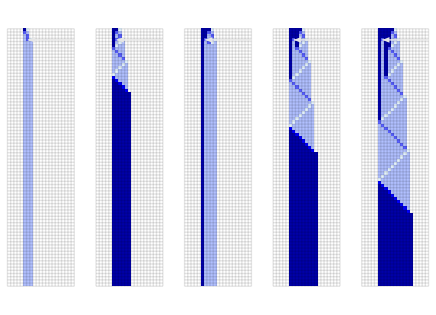

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Medium],GrayLevel[.9], Haloing[Red, 1.25]],"ArrowDirection"->Left,"InitialIndex"->0, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[2]]
]
```

## Exploring the Model: A More Efficient Procedure

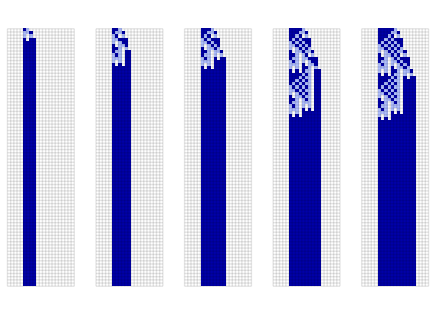

```mathematica
SeedRandom[111000+8];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{30,9}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[1]]
]
```

## Exploring the Model: A More Efficient Procedure

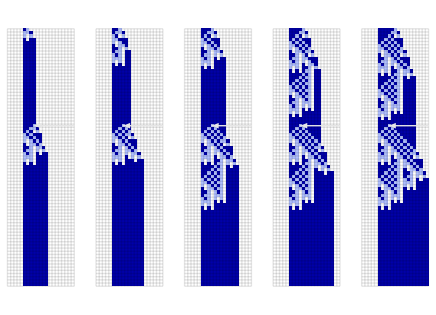

```mathematica
SeedRandom[111000+8];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{30,9}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Medium],GrayLevel[.9], Haloing[Red, 1]],"ArrowDirection"->Left,"InitialIndex"->0, ImageSize->{Automatic, 300}]]@@@#]&@caperts[[2]]
]
```

## A Larger Attack Surface: Perturbing the Rules

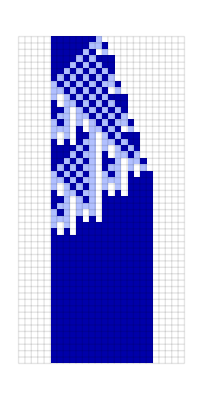

```mathematica
GraphicsRow[{RulePlot[CellularAutomaton[{837428508144, 3, 1}],ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}], ArrayPlot[CellularAutomaton[{837428508144, 3, 1},{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, Mesh->True, MeshStyle->Opacity[.1]]}, ImageSize->{Automatic, 300}]
```

## A Larger Attack Surface: Perturbing the Rules

```mathematica
RuleSequencePlot[{n_, k_, r_}, ops:OptionsPattern[{ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= 
ArrayPlot[{IntegerDigits[n, k, k^(2r+1)]},ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize], ops]
```

```mathematica
Module[{rule ={837428508144, 3, 1},sp,cf, is, murule = {837471554865,3,1}},
is = {200, Automatic};
 sp = RuleSequencePlot[rule,ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]},  ImageSize->is]; 
GraphicsRow[GraphicsColumn/@
{{sp, ArrayPlot[CellularAutomaton[rule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, ImageSize->is, Mesh->True, MeshStyle->Opacity[.1]]},
{Show[RuleSequencePlot[murule,ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]},  ImageSize->is],
With[{loc = SparseArray[{Subtract@@(IntegerDigits[#1, #2, #2^(2#3+1)]&@@@{murule, rule})}]["ExplicitPositions"][[1, 2]] -.5},
Graphics[{Style[Text["Compromise", {loc, 12}], Italic],Red, Arrowheads[.085],Thick,Arrow[{{loc , 10}, {loc, 1}}]}]]
, ImageSize->is],
ArrayPlot[CellularAutomaton[murule,{Append[Table[1, 7], 2],0},{50,{-5, 20}}], ColorRules->{0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, ImageSize->is, Mesh->True, MeshStyle->Opacity[.1]]}
}, Alignment->Bottom]]
```

-Graphics-

## A Larger Attack Surface: Perturbing the Rules

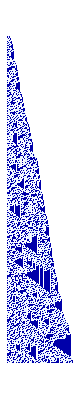

```mathematica
GraphicsRow[Table[
SeedRandom[111170+30];ArrayPlot[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[{837428508144, 3, 1}],{Join[Table[1,4],{2}],0},{{1000*i, 1000*(i+1)},Automatic}], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]],{i,0, 4}] , ImageSize->{275, Automatic}]
```

#### Bottom Line: Computational irreducibility is what makes computer security challenging

## Future Work: More Sophisticated Software Systems

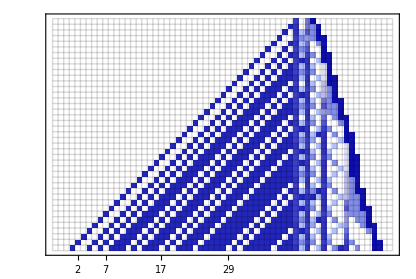

```mathematica
With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0}},Show[ArrayPlot[CellularAutomaton[rule,init,{{0,40},{-43,17}}],Mesh->True,MeshStyle->Opacity[.15],ImageSize->500, ColorFunction->(Blend[{White,Darker[Blue], RGBColor[0.696, 0.752, 1]}, #]&), TicksStyle->GrayLevel[.25],Frame->True,FrameTicksStyle->GrayLevel[.25],FrameTicks->{False, Table[{Prime[i] + 3, Prime[i]}, {i, 1,12}], False, False}]]]
```

## Future Work: Cellular Automata Cryptocurrency